Spot Assay Processor

The Mathematica “Spot Assay Processor” notebook is designed to quantify colony growth on solid media plates under different environment factors from pictures taken from the incubation at regular intervals. The colonies are laid out on a matrix using a “spotting” technique commonly having rows for the different strains or mutants of the organisms under study and a dilution series as columns.

The notebook processes these images in the following successive steps:

Detect colonies on the background using a sequence of image processing techniques:

Convert the image to a grayscale representation.

Tophat Transform filter to equalize possible uneven illumination in the image. Uses tophatr variable as threshold.

Threshold filter to better define colonies and boundaries between colony and medium. This filter uses cluster variance maximization (Otsu’s algorithm) to perform automatic clustering-based image thresholding on grayscale images.

Binarization to convert the pixels of the detected colonies to 1 (white) and background pixels to 0 (black).

Isolate the colonies in the image by partitioning the image into a matrix according to the imagematrix variable (columns x rows). The partitioning scheme uses padding to ensure that each partition is of equal pixels size and corrects to some extend possible misalignment of colonies in the matrix cells. The latter prevents the edges of one colony to flow over into the matrix cell of another colony leading to false positives in colony pixel counts.

Count the 1’s in the binary matrices after partitioning as a metric for colony growth.

In case of a reference plate, the pixel counts in the assay are normalized by the pixel counts in the reference. This may lead the less pixels than the reference image in which case the organisms growth rate is reduced (sensitivity) under influence of the environmental factor, no effect or more pixels in which case colony growth in increased under influence of the environmental factor. This notebook focuses on sensitivity and therefor all pixel counts higher than the control are set to equal the control (growth cannot be higher than the control).

In case of a control image, a final value for sensitivity is calculated by averaging the difference in growth over the dilution series.

```mathematica
Program usage
```

The interactive notebook will ask you to define one or multiple image files to process and optionally a reference image.

Program settings

/Users/mvdijk/Desktop/angelina/apap-50-slide1.png

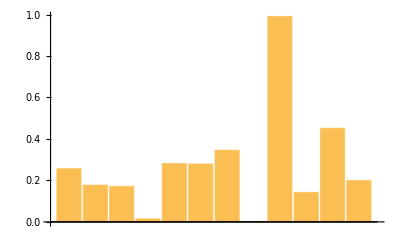

/Users/mvdijk/Desktop/angelina/apap-60-slide1.png

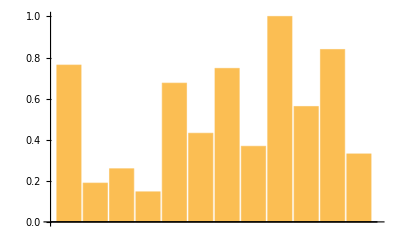

/Users/mvdijk/Desktop/angelina/apap-70-slide1.png

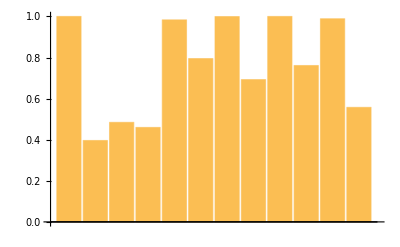

```mathematica
imagematrix={4,12};
padding = 0.2;
tophatr = 20;

(*SELECTING FILES*)
imagepaths =  SystemDialogInput["FileOpen", WindowTitle->"Select one or multiple image files"];
controlimagepath = SystemDialogInput["FileOpen", WindowTitle->"Select a control image"];
outputexcelpath = FileNameJoin[{NotebookDirectory[], "spottingdata.xls"}];

(*ensure controle image paths is one path, and imagepaths is a list*)
controlimagepath = First[List[controlimagepath]];
imagepaths = Flatten[List[imagepaths]];

(*FUNCTIONS*)
(*Count all pixels not black (0)*)
CountWhite = Function[i,Count[Flatten[ImageData@i],x_/;x>0.]];

(*pre-process image: remove uneven field illumination, binarize image*)
ProcessImage = Function[img,
Binarize[Threshold[TopHatTransform[ColorConvert[img, "Grayscale"],tophatr], {"Hard","Cluster"}]]
];

(*Partition image and count white pixels*)
imagematrix[[2]] - padding;  (*apply bit of padding to the column height*)
PartitionAndCount= Function[img,
Map[CountWhite, ImagePartition[img,ImageDimensions[img]/imagematrix, Padding->Black ], {2}]
];

(*Replace all values largen than 0 by 0*)
PositiveReplace[x_]:=If[x>0,0,x];
SetAttributes[PositiveReplace,Listable];

(*MAIN ROUTINE*)
(*Import and process control image file*)
control = ProcessImage[Import[controlimagepath]];
controlcount = PartitionAndCount[control];
nocontrol = False;
(*If[Length[controlimagepath],
(
control = ProcessImage[Import[controlimagepath]];
controlcount = PartitionAndCount[control];
nocontrol = False
),
nocontrol = True;
];*)

collecteddata = {};
For[i=1,i≤Length[imagepaths ],i++,
assay = ProcessImage[Import[imagepaths [[i]]]];

(*Partition image and count white pixels*)
assaycount = PartitionAndCount[assay];

(*Normalize assay dilution series with respect control dilution series
if there is a control image defined*)
If[nocontrol,whitecount = assaycount, whitecount = (assaycount-controlcount)/controlcount];

(*Replace all normalized count differces larger than 0 by 0. For sensitivity data, growth should not be more than control*)
whitecount =PositiveReplace[whitecount];

(*Average of absolute values in the series. If 0 than case not sensitive for condition
if 1 then fully sensitive (no growth)*)
sensitivity = N[Abs[(Map[Total,whitecount,{1}])/imagematrix[[1]]]];
AppendTo[collecteddata, sensitivity];
Print[imagepaths [[i]]];
Print[BarChart[sensitivity]];
]

collecteddata = Transpose[collecteddata];
filenames = Map[FileBaseName, imagepaths ];
Export[outputexcelpath,PrependTo[collecteddata, filenames], "XLS"];
```